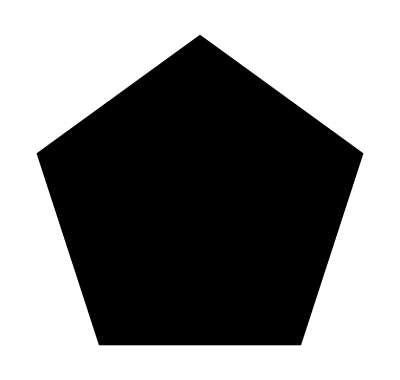

```mathematica
Show[Graphics[RegularPolygon[5],AspectRatio->Automatic]]
```

center at (0,0)
original vertex point sets

```mathematica
a1 = Cos[2π/5];
b1 = Cos[π/5];
c1 = Sin[2π/5];
d1 = Sin[4π/5];
vertices={{a1,-c1}, {1,0}, {a1,c1}, {-b1,d1}, {-b1,-d1}};
transv1 = {{a1+1,-c1}, {1+1,0}, {a1+1,c1}, {-b1+1,d1}, {-b1+1,-d1}};
```

n = 1

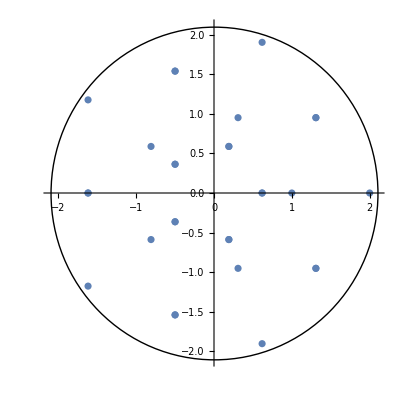

```mathematica
rotv1 = RotationTransform[2π/5, {0,0}] /@ # &@transv1;
rotv2 = RotationTransform[2π/5, {0,0}] /@ # &@rotv1;
rotv3 = RotationTransform[2π/5, {0,0}] /@ # &@rotv2;
rotv4 = RotationTransform[2π/5, {0,0}] /@ # &@rotv3;
n1point = ListPlot[Join[vertices, transv1, rotv1, rotv2, rotv3, rotv4], AspectRatio->1];
circle = Graphics[Circle[{0, 0}, 2.1]];
n1 = Show[n1point, circle, PlotRange-> All]
```

n = 2

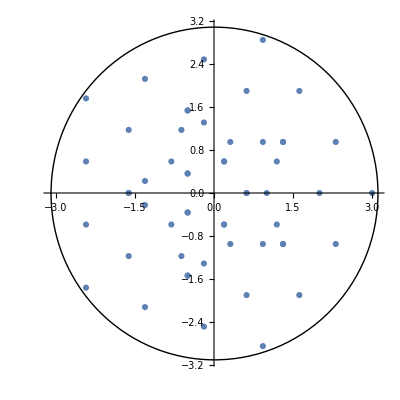

```mathematica
a1 = Cos[2π/5];
b1 = Cos[π/5];
c1 = Sin[2π/5];
d1 = Sin[4π/5];
vertices={{a1,-c1}, {1,0}, {a1,c1}, {-b1,d1}, {-b1,-d1}};
transv1 = {{a1+1,-c1}, {1+1,0}, {a1+1,c1}, {-b1+1,d1}, {-b1+1,-d1}};
rotv1 = RotationTransform[2π/5, {0,0}] /@ # &@transv1;
rotv2 = RotationTransform[2π/5, {0,0}] /@ # &@rotv1;
rotv3 = RotationTransform[2π/5, {0,0}] /@ # &@rotv2;
rotv4 = RotationTransform[2π/5, {0,0}] /@ # &@rotv3;
transv2 = {{a1+2,-c1}, {1+2,0}, {a1+2,c1}, {-b1+2,d1}, {-b1+2,-d1}};
rotv5 = RotationTransform[2π/5, {0,0}] /@ # &@transv2;
rotv6 = RotationTransform[2π/5, {0,0}] /@ # &@rotv5;
rotv7 = RotationTransform[2π/5, {0,0}] /@ # &@rotv6;
rotv8 = RotationTransform[2π/5, {0,0}] /@ # &@rotv7;
n2point = ListPlot[Join[vertices, transv1, rotv1, rotv2, rotv3, rotv4, transv2, rotv5, rotv6, rotv7, rotv8], AspectRatio->1];
circle2 = Graphics[Circle[{0, 0}, 3.1]];
n2 = Show[n2point, circle2, PlotRange-> All]
```

```mathematica
set = ListPlot[Join[vertices, transv1, rotv1, rotv2, rotv3, rotv4, transv2, rotv5, rotv6, rotv7, rotv8], Axes-> False, AspectRatio->1];
{width,height}=ImageDimensions[n2];
w=40;h=45;
hexgrid=ImageTake[n2,{h,height-h},{w,width-w}];
ParametricPlot3D[{Cos[u] Sin[v],Sin[u] Sin[v],Cos[v]},{u,0,2 Pi},{v,0,Pi},Mesh->None,PlotPoints->100,Boxed->False,PlotStyle->Texture[Show[n2,ImageSize->1000]],Axes->False,RotationAction->"Clip",ViewPoint->{-2.026774,2.07922,1.73753418},ImageSize->600]
```

-Graphics3D-

```mathematica
VertexList[PolyhedronData["Icosidodecahedron"]]
```

VertexList::graph: A graph object is expected at position 1 in ….

VertexList[-Graphics3D-]

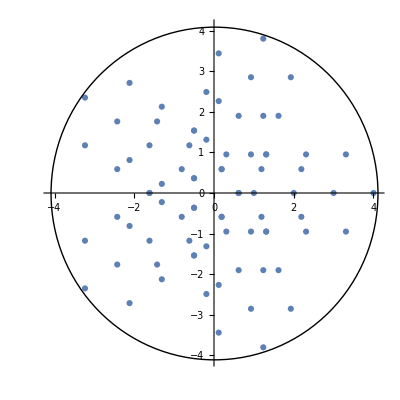

```mathematica
a1 = Cos[2π/5];
b1 = Cos[π/5];
c1 = Sin[2π/5];
d1 = Sin[4π/5];
vertices={{a1,-c1}, {1,0}, {a1,c1}, {-b1,d1}, {-b1,-d1}};
transv1 = {{a1+1,-c1}, {1+1,0}, {a1+1,c1}, {-b1+1,d1}, {-b1+1,-d1}};
rotv1 = RotationTransform[2π/5, {0,0}] /@ # &@transv1;
rotv2 = RotationTransform[2π/5, {0,0}] /@ # &@rotv1;
rotv3 = RotationTransform[2π/5, {0,0}] /@ # &@rotv2;
rotv4 = RotationTransform[2π/5, {0,0}] /@ # &@rotv3;
transv2 = {{a1+2,-c1}, {1+2,0}, {a1+2,c1}, {-b1+2,d1}, {-b1+2,-d1}};
rotv5 = RotationTransform[2π/5, {0,0}] /@ # &@transv2;
rotv6 = RotationTransform[2π/5, {0,0}] /@ # &@rotv5;
rotv7 = RotationTransform[2π/5, {0,0}] /@ # &@rotv6;
rotv8 = RotationTransform[2π/5, {0,0}] /@ # &@rotv7;
transv3 = {{a1+3,-c1}, {1+3,0}, {a1+3,c1}, {-b1+3,d1}, {-b1+3,-d1}};
rotv9 = RotationTransform[2π/5, {0,0}] /@ # &@transv3;
rotv10 = RotationTransform[2π/5, {0,0}] /@ # &@rotv9;
rotv11 = RotationTransform[2π/5, {0,0}] /@ # &@rotv10;
rotv12 = RotationTransform[2π/5, {0,0}] /@ # &@rotv11;
n2point = ListPlot[Join[vertices, transv1, rotv1, rotv2, rotv3, rotv4, transv2, rotv5, rotv6, rotv7, rotv8,transv3, rotv9, rotv10, rotv11, rotv12], AspectRatio->1];
circle2 = Graphics[Circle[{0, 0}, 4.1]];
n2 = Show[n2point, circle2, PlotRange-> All]
```

```mathematica
Show[PolyhedronData["Icosahedron"], Sphere]
```

Show::gcomb: Could not combine the graphics objects in ….

Show[-Graphics3D-,Sphere]